```mathematica
l=16;
ll=ToString[l];
d=0.221654;
histd[d][l]={}
Do[

ii=ToString[i];
data[i][l]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/Ising/ising-EnergyHistogram-l"<>ll<>"-k0.221654-run"<>ii<>".txt",Number];
histd[d][l]=Join[histd[d][l],data[i][l]];
,{i,{1,2,3,4,5}}
]
```

{}

$Aborted

```mathematica
pdfl[d][l]=HistogramList[histd[d][l],{-8000,-2000,4},"PDF"];
pdf[d][l]=Table[{(pdfl[d][l][[1]][[i]]+pdfl[d][l][[1]][[i+1]])/2.0,4*pdfl[d][l][[2]][[i]]},{i,1,Length[pdfl[d][l][[2]]]}];
```

```mathematica
l=16;
ll=ToString[l];
Do[
dd=ToString[d];
histd[d][l]={};
Do[

ii=ToString[i];
data[i][l]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/Ising/ising-EnergyHistogram-l"<>ll<>"-k"<>dd<>"-run"<>ii<>".txt",Number];
histd[d][l]=Join[histd[d][l],data[i][l]];
,{i,{1,2,3,4,5}}
]
,{d,{0.21,0.214,0.218,0.222,0.226,0.23,0.234,0.221654}}
]
```

```mathematica
Do[
pdfl[d][l]=HistogramList[histd[d][l],{-8000,-2000,4},"PDF"];
pdf[d][l]=Table[{(pdfl[d][l][[1]][[i]]+pdfl[d][l][[1]][[i+1]])/2.0,4*pdfl[d][l][[2]][[i]]},{i,1,Length[pdfl[d][l][[2]]]}];
,{d,{0.21,0.214,0.218,0.222,0.226,0.23,0.234,0.221654}}
]
```

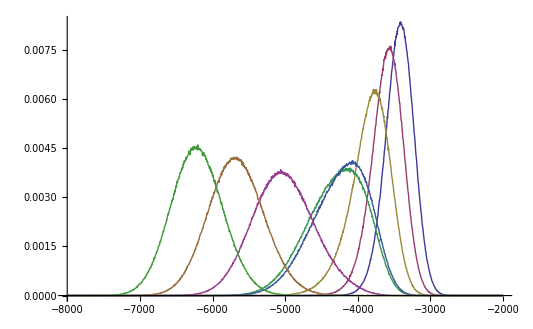

```mathematica
ListLinePlot[{pdf[0.21][l],pdf[0.214][l],pdf[0.218][l],pdf[0.222][l],pdf[0.221654][l],pdf[0.226][l],pdf[0.23][l],pdf[0.234][l]},PlotRange->Full]
```

```mathematica
k0=0.221654;
k=0.224;
z[k][l]=Sum[pdf[k0][l][[All,2]][[i]]*Exp[(k0-k)*pdf[k0][l][[All,1]][[i]]],{i,1,Length[pdf[k0][l]]}]
h[k][l]=Table[{pdf[k0][l][[All,1]][[i]],pdf[k0][l][[All,2]][[i]]*Exp[(k0-k)*pdf[k0][l][[All,1]][[i]]]/z[k][l]},{i,1,Length[pdf[k0][l]]}];
```

32833.2

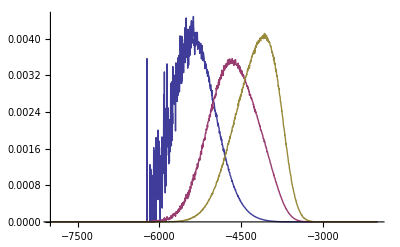

```mathematica
ListLinePlot[{h[0.228][l],h[0.224][l],pdf[k0][l]},PlotRange->Full]
```

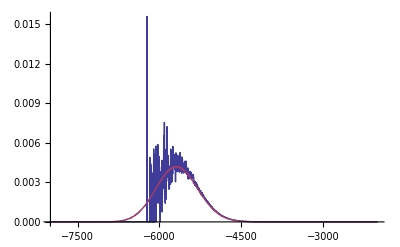

```mathematica
ListLinePlot[{h[0.23][l],pdf[0.23][l]},PlotRange->Full]
```

```mathematica
k0=0.221654;
k=0.23;
z[k][l]=Sum[pdf[k0][l][[All,2]][[i]]*Exp[(k0-k)*pdf[k0][l][[All,1]][[i]]],{i,1,Length[pdf[k0][l]]}]
h[k][l]=Table[{pdf[k0][l][[All,1]][[i]],pdf[k0][l][[All,2]][[i]]*Exp[(k0-k)*pdf[k0][l][[All,1]][[i]]]/z[k][l]},{i,1,Length[pdf[k0][l]]}];
```

```mathematica
hm[k][l]=Table[{pdf[k0][l][[All,1]][[i]],pdf[k0][l][[All,2]][[i]]*Exp[k0*pdf[k0][l][[All,1]][[i]]]/z[k][l]},{i,1,Length[pdf[k0][l]]}]
```

```mathematica
ClearAll[k]
j=1;
k[j]=0.21;
f[k[j]]=Sum[pdf[k[j]][l][[All,2]][[i]],{i,1,Length[pdf[k[j]][l]]}]
```

1

```mathematica
k[1]=0.21;
k[2]=0.214;
k[3]=0.218;
k[4]=0.222;
k[5]=0.226;
k[6]=0.23;
k[7]=0.221654;
Do[
f[k[j]]=Sum[pdf[k[j]][l][[All,2]][[i]],{i,1,Length[pdf[k[j]][l]]}]
,{j,{1,2,3,4,5,6,7}}
]
```

```mathematica
f[k[7]]
```

1

```mathematica
For[x=0.21,x<0.2305,x+=0.01,
```

```mathematica
x=0.23;
k0=0.221654;

in=4;
fi=6;

z[x][l]=Sum[pdf[k0][l][[All,2]][[i]]*Exp[(k0-x)*pdf[k0][l][[All,1]][[i]]],{i,1,Length[pdf[k0][l]]}]
h[x][l]=Table[{pdf[k0][l][[All,1]][[i]],pdf[k0][l][[All,2]][[i]]*Exp[(k0-x)*pdf[k0][l][[All,1]][[i]]]/z[x][l]},{i,1,Length[pdf[k0][l]]}];


haux[x][l]=Table[{pdf[k[1]][l][[All,1]][[i]],Sum[pdf[k[j]][l][[All,2]][[i]]*Exp[-x*pdf[k[1]][l][[All,1]][[i]]],{j,in,fi}]/Sum[Exp[-k[j]*pdf[k[j]][l][[All,1]][[i]]]/f[k[j]],{j,in,fi}]},{i,1,Length[pdf[k[1]][l]]}];
nor[x][l]=Sum[haux[x][l][[All,2]][[i]],{i,1,Length[haux[x][l]]}];
hm[x][l]=Table[{haux[x][l][[All,1]][[i]],haux[x][l][[All,2]][[i]]/nor[x][l]},{i,1,Length[haux[x][l]]}];


e[x]=Sum[h[x][l][[All,1]][[i]]*h[x][l][[All,2]][[i]],{i,1,Length[h[x][l]]}];
e2[x]=Sum[(h[x][l][[All,1]][[i]]^2)*h[x][l][[All,2]][[i]],{i,1,Length[h[x][l]]}];
c[x]=x^2*(e2[x]-e[x]^2);
em[x]=Sum[hm[x][l][[All,1]][[i]]*hm[x][l][[All,2]][[i]],{i,1,Length[hm[x][l]]}]
e2m[x]=Sum[(hm[x][l][[All,1]][[i]]^2)*hm[x][l][[All,2]][[i]],{i,1,Length[hm[x][l]]}];
cm[x]=x^2*(e2m[x]-em[x]^2);
```

9.77714×10^17

-4992.78

0.23

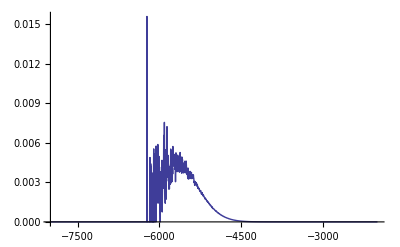

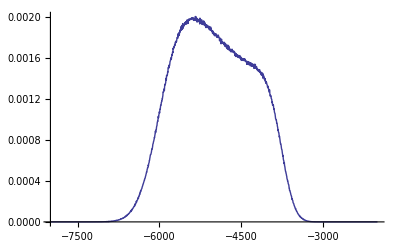

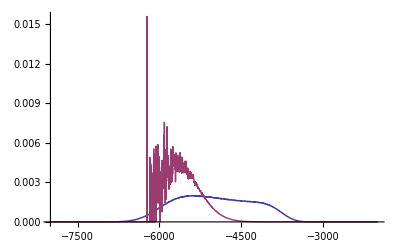

```mathematica
x=0.23
ListLinePlot[{h[x][l]},PlotRange->Full]
ListLinePlot[{hm[x][l]},PlotRange->Full]
ListLinePlot[{hm[x][l],h[x][l]},PlotRange->Full]
```

```mathematica
ClearAll[Energy,Energym,HC,HCm]
Energy[l]=Table[{k,e[k]},{k,0.21,0.23,0.001}]
Energym[l]=Table[{k,em[k]},{k,0.21,0.23,0.001}]
HC[l]=Table[{k,c[k]},{k,0.21,0.23,0.001}]
HCm[l]=Table[{k,cm[k]},{k,0.21,0.23,0.001}]
```

```mathematica
Energy[l]={{0.21,-3424.500988565357},{0.211,-3464.5157301683457},{0.212,-3506.3695382448254},{0.213,-3550.4768455673875},{0.214,-3597.431331655956},{0.215,-3648.0776975642534},{0.216,-3703.624670242839},{0.217,-3765.8101699826902},{0.218,-3837.11335083062},{0.219,-3920.9507408292952},{0.22,-4021.6506947123466},{0.221,-4143.765828874051},{0.222,-4290.205452983622},{0.223,-4459.4663700866695},{0.224,-4644.1381073617795},{0.22499999999999998,-4833.256926242345},{0.22599999999999998,-5017.179975555312},{0.22699999999999998,-5190.319196203865},{0.22799999999999998,-5350.105260091322},{0.22899999999999998,-5494.777859140344},{0.22999999999999998,-5622.458065888757}};
```

```mathematica
Energym[l]={{0.21,-2848.244023039161},{0.211,-2874.3367407098735},{0.212,-2900.8427889367854},{0.213,-2927.800670596743},{0.214,-2955.2727447003867},{0.215,-2983.341699583005},{0.216,-3012.109181252215},{0.217,-3041.6969195073384},{0.218,-3072.250673469909},{0.219,-3103.947635222216},{0.22,-3137.008693928784},{0.221,-3171.7185035535886},{0.222,-3208.4595605651457},{0.223,-3247.774215902446},{0.224,-3290.489300011479},{0.22499999999999998,-3338.002278722338},{0.22599999999999998,-3393.0592357569712},{0.22699999999999998,-3462.319798881986},{0.22799999999999998,-3566.3954853555692},{0.22899999999999998,-3779.849346598881},{0.22999999999999998,-4307.3051841783135}};
```

```mathematica
HC[l]={{0.21,1728.6254551658485},{0.211,1819.912317193638},{0.212,1928.0247510452853},{0.213,2060.3885283748614},{0.214,2227.237450682363},{0.215,2443.3402175248143},{0.216,2730.4211067149486},{0.217,3120.026913986137},{0.218,3655.4063920958006},{0.219,4387.903996580076},{0.22,5357.917214153887},{0.221,6547.921610888806},{0.222,7816.257735962253},{0.223,8883.996883333586},{0.224,9471.80509480145},{0.22499999999999998,9507.836341162418},{0.22599999999999998,9149.332462236196},{0.22699999999999998,8593.073197352604},{0.22799999999999998,7929.22985382916},{0.22899999999999998,7157.551422752877},{0.22999999999999998,6274.542032684199}};
```

```mathematica
HCm[l]={{0.21,1141.8346471480181},{0.211,1170.6881235999492},{0.212,1201.056979429096},{0.213,1234.1640976611282},{0.214,1271.0747270283346},{0.215,1312.7754532147264},{0.216,1360.2790981289982},{0.217,1414.7488587324071},{0.218,1477.6492145137593},{0.219,1550.9495185410988},{0.22,1637.4348307764865},{0.221,1741.235701936026},{0.222,1868.825191783613},{0.223,2031.1029034516607},{0.224,2248.329975137896},{0.22499999999999998,2563.718528084471},{0.22599999999999998,3087.933838549005},{0.22699999999999998,4172.3647733621865},{0.22799999999999998,7160.033527306914},{0.22899999999999998,17066.152185860225},{0.22999999999999998,39727.31222736033}};
```

```mathematica
x=0.23
e[x]
em[x]
c[x]
cm[x]
```

0.23

-5622.46

-4307.31

6274.54

39727.3

```mathematica
0.23
```

0.23

```mathematica
0.229
```

0.229

```mathematica
0.227
```

0.227

```mathematica
e[0.21]
```

$Aborted[]

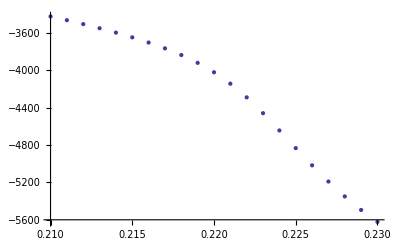

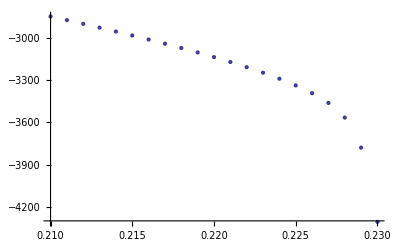

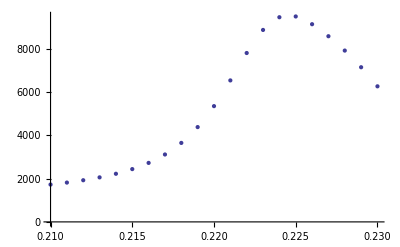

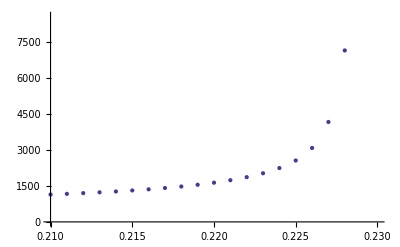

```mathematica
ListPlot[Energy[l]]
ListPlot[Energym[l]]
ListPlot[HC[l]]
ListPlot[HCm[l]]
```